```mathematica
SetDirectory["/Users/teh1m/chem:stat3240/stats/StatsProjFa16/mathematica"]
```

/Users/teh1m/chem:stat3240/stats/StatsProjFa16/mathematica

xc          yc          oa       oaRef

--------------------------------------------

UPPER RIGHT

UPPER RIGHT

UPPER RIGHT

«2 more identical outputs»

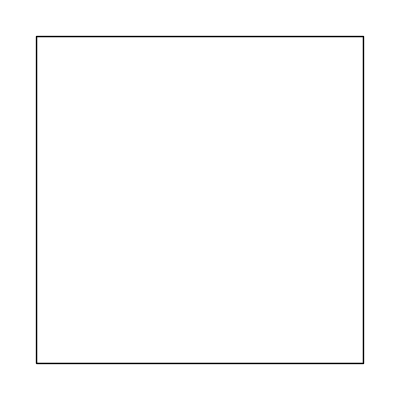

```mathematica
SetDirectory[NotebookDirectory[]];
csv=Import["area-check.csv"];


csv=Delete[csv,1];
{xd,yd}=Dimensions[csv];
xc=csv[[All,1]];
yc=csv[[All,2]];
oa3=csv[[All,3]];

r=37;

oa=ConstantArray[0,xd];

xc1={};
yc1={};
Print["   xc          yc          oa       oaRef"];
Print["--------------------------------------------"];
Do[
oa[[k]]=overlapArea[xc[[k]],yc[[k]],r];
If[Abs[oa[[k]]-oa3[[k]]]>0.1,
Print[PaddedForm[xc[[k]],6],"    ",PaddedForm[yc[[k]],6],"    ",PaddedForm[oa[[k]],6],"    ",PaddedForm[oa3[[k]],6]];
AppendTo[xc1,xc[[k]]];
AppendTo[yc1,yc[[k]]];
];

,{k,xd}];


stand=Line[{{0,0},{0,750},{750,750},{750,0},{0,0}}];
circles={};
Do[
AppendTo[circles,Circle[{xc1[[k]],yc1[[k]]},r]]
,{k,Length[xc1]}];
Show[Graphics[circles],Graphics[stand]]
```